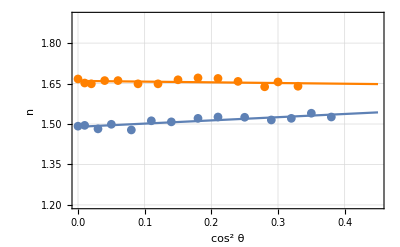

```mathematica
o={{0, 1.667}, {0.01, 1.652}, {0.02, 1.649}, {0.04, 1.661}, {0.06, 1.661}, {0.09, 1.649}, {0.12, 1.649}, {0.15, 1.664}, {0.18, 1.671}, {0.21, 1.669}, {0.24, 1.658}, {0.28, 1.638}, {0.3, 1.656}, {0.33, 1.640}};
e={{0, 1.492}, {0.01, 1.495}, {0.03, 1.482}, {0.05, 1.499}, {0.08, 1.478}, {0.11, 1.512}, {0.14, 1.508}, {0.18, 1.521}, {0.21, 1.526}, {0.25, 1.525}, {0.29, 1.515}, {0.32, 1.521}, {0.35, 1.540}, {0.38, 1.526}};
ApproxO=LinearModelFit[o,x,x];
ApproxO=ApproxO["BestFit"];
ApproxE=LinearModelFit[e,x,x];
ApproxE=ApproxE["BestFit"];
Show[ListPlot[o, PlotTheme->"Detailed", PlotMarkers->Automatic, PlotStyle->Orange],ListPlot[e,PlotTheme->"Detailed",PlotMarkers->Automatic],Plot[ApproxO, {x,0,0.45},PlotStyle->Orange], Plot[ApproxE,{x,0,0.45}],PlotRange->{1.2,1.9},FrameLabel->{{HoldForm[n],None},{HoldForm[cos^2 θ],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```